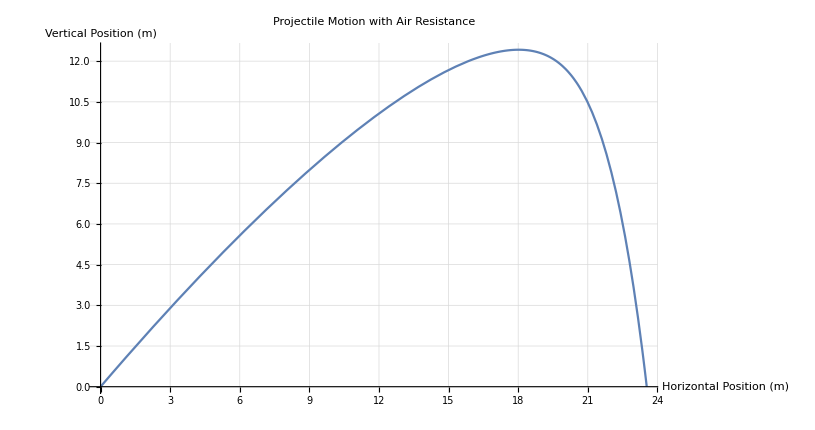

```mathematica
(*Define constants and parameters*)g=9.8;(*gravitational acceleration*)m=0.1;(*mass of the projectile*)c=0.1;(*air resistance coefficient*)v0=30;(*initial velocity*)angle=π/4;
MaxFallTime = 40;
MinFallTime = 0.1;

eqns={
m*x''[t]==-c*x'[t]*x'[t]/Sqrt[y'[t]^2+x'[t]^2],
m*y''[t]==-c*y'[t]*y'[t]/Sqrt[y'[t]^2+x'[t]^2]-m*g
};


ics={x[0]==0,
y[0]==0,
y'[0]==v0*Sin[angle],
x'[0]==v0*Cos[angle]
};


sol=NDSolve[Join[eqns,ics],{x,y,v,θ},{t,0,MaxFallTime}];


{xSol,ySol, vxSol, vySol, axSol, aySol}={x[t],y[t],x'[t],y'[t],x''[t],y''[t]}/.sol[[1]];

timeOfFlight=t/.FindRoot[ySol==0,{t,MinFallTime,MaxFallTime}];

ParametricPlot[{xSol,ySol},{t,0,timeOfFlight},AspectRatio->Automatic,PlotLabel->"Projectile Motion with Air Resistance",AxesLabel->{"Horizontal Position (m)","Vertical Position (m)"},GridLines->Automatic]

Plot[{Sqrt[vxSol^2+vySol^2]},{t,0,timeOfFlight},PlotLabel->"Projectile Motion with Air Resistance",AxesLabel->{"Time (s)","Velocity (m/s)"},GridLines->Automatic];

Plot[{ArcCos[vxSol/Sqrt[vxSol^2+vySol^2]]},{t,0,timeOfFlight},PlotLabel->"Projectile Motion with Air Resistance",AxesLabel->{"Time(s)","Angle"},GridLines->Automatic];

Plot[{Sqrt[axSol^2+aySol^2]},{t,0,timeOfFlight},PlotLabel->"Projectile Motion with Air Resistance",AxesLabel->{"Time(s)","Asseleration (m/s^2)"},GridLines->Automatic];
```

```mathematica
(*Define constants and parameters*)g=9.8;(*gravitational acceleration*)m=0.1;(*mass of the projectile*)v0=30;(*initial velocity*)angle=π/4;
SetDirectory[NotebookDirectory[]];
MaxFallTime=40;
MinFallTime=0.1;

Export["ProjectileMotion.gif",
Animate[(*Air resistance coefficient varying from 0 to 0.5*)c=currentC;
eqns={m*x''[t]==-c*x'[t]*x'[t]/Sqrt[y'[t]^2+x'[t]^2],m*y''[t]==-c*y'[t]*y'[t]/Sqrt[y'[t]^2+x'[t]^2]-m*g};
ics={x[0]==0,y[0]==0,y'[0]==v0*Sin[angle],x'[0]==v0*Cos[angle]};
sol=NDSolve[Join[eqns,ics],{x,y,v,θ},{t,0,MaxFallTime}];
{xSol,ySol}={x[t],y[t]}/.sol[[1]];
timeOfFlight=t/.FindRoot[ySol==0,{t,MinFallTime,MaxFallTime}];
ParametricPlot[{xSol,ySol},{t,0,timeOfFlight},AspectRatio->Automatic,PlotLabel->"Projectile Motion with Air Resistance",AxesLabel->{"Horizontal Position (m)","Vertical Position (m)"},GridLines->Automatic],{{currentC,0,"Air Resistance Coefficient"},0,0.5,0.01,Appearance->"Labeled",ControlType->Slider,ImageSize->Medium,AppearanceElements->{"StepLeftButton","StepRightButton","PlayPauseButton","FasterSlowerButtons"}},AnimationRepetitions->1
]
]
```

ProjectileMotion.gif